```mathematica
(* Plotting Package *)
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts}"}];
rasterListContourPlot[pList_,opts:OptionsPattern[]]:=Module[{img,cont,contL,plotRangeRule,contourOptions,frameOptions,rangeCoords},contourOptions=Join[FilterRules[{opts},FilterRules[Options[ListContourPlot],Except[{Background,Frame,Axes}]]],{Frame->None,Axes->None}];
contL=ListContourPlot[pList,Evaluate@Apply[Sequence,contourOptions]];
cont=First[Cases[{contL},Graphics[__],Infinity]];
img=Rasterize[Graphics[GraphicsComplex[cont[[1,1]],cont[[1,2,1]]],PlotRangePadding->None,ImagePadding->None,Options[cont,PlotRange]],"Image",ImageSize->With[{size=Total[{2,0} (ImageSize/.{opts})/.{ImageSize->CurrentValue[ImageSize]}]},If[NumericQ[size],size,First[WindowSize/.Options[EvaluationNotebook[]]]]]];
plotRangeRule=FilterRules[AbsoluteOptions[cont],PlotRange];
rangeCoords=Transpose[PlotRange/.plotRangeRule];
frameOptions=Join[FilterRules[{opts},FilterRules[Options[Graphics],Except[{PlotRangeClipping,PlotRange}]]],{plotRangeRule,Frame->True,PlotRangeClipping->True}];
If[Head[contL]===Legended,Legended[#,contL[[2]]],#]&@Show[Graphics[{Inset[Show[SetAlphaChannel[img,"ShadingOpacity"/.{opts}/.{"ShadingOpacity"->1}],AspectRatio->Full],rangeCoords[[1]],{0,0},rangeCoords[[2]]-rangeCoords[[1]]]},PlotRangePadding->None],Graphics[GraphicsComplex[cont[[1,1]],cont[[1,2,2]]]],Evaluate@Apply[Sequence,frameOptions]]]
(* These functions can basically be ignored. It's just dealing with the graphics for when I want to format my publication-quality plots. *)
Clear[undistortedGraphicsColumn];
Options[undistortedGraphicsColumn]=Join[{Spacings->0},Options[Graphics]];
undistortedGraphicsColumn[list_, opts:OptionsPattern[]]:=Module[{sizes=ImageDimensions/@list,width, xsizes, ysizes},width=Max@sizes[[All,1]];
ysizes=sizes[[All,2]]+Join[{0},ConstantArray[OptionValue[Spacings],Length@list-1]];
xsizes = sizes[[All, 1]];
Graphics[Table[Inset[list[[i]],{(width - xsizes[[i]]) / 2,-Plus@@ysizes[[;;i]]},ImageScaled[{0,0}]],{i,Length[list]}],ImageSize->{width,Plus@@ysizes},ImagePadding->None,PlotRange->{{0,width},{-Plus@@ysizes,0}},AspectRatio->Plus@@ysizes/width,PlotRangePadding->None]]

Clear[undistortedGraphicsRow];
Options[undistortedGraphicsRow]=Join[{Spacings->0},Options[Graphics]];
undistortedGraphicsRow[list_, opts:OptionsPattern[]]:=Module[{sizes=ImageDimensions/@list,height, xsizes, ysizes},height=Max@sizes[[All,2]];
xsizes=sizes[[All,1]]+Join[ConstantArray[OptionValue[Spacings],Length@list-1],{0}];
ysizes = sizes[[All, 2]];
Graphics[Table[Inset[list[[i]],{If[i>1, Plus@@xsizes[[;;i-1]],0], (height-ysizes[[i]])/2},ImageScaled[{0,0}]],{i,Length[list]}],ImageSize->{Plus@@xsizes, height},ImagePadding->None,PlotRange->{{0, Plus@@xsizes}, {0, height}},AspectRatio->height/(Plus@@xsizes),PlotRangePadding->None]]

Clear[format]
Options[format] = Options[PaddedForm];
format[x_, sd_]:=Module[{m,e},
{m,e} = MantissaExponent[x];
If[x == 0, "0",If[-2≤e≤2,ToString[PaddedForm[x, sd]],ToString[PaddedForm[ToExpression[ToString[m]]*10, sd]]<>"\\times10^{"<>ToString[e-1]<>"}"]]
]
```

```mathematica
(*This part is for chooing a nice zoom in trajectory for illustration*)
(*Intersection[Flatten[Position[Transpose[Simpoints][[2]],_?(#<-4&)]],Flatten[Position[Transpose[Simpoints][[2]],_?(#<-8&)]],
Flatten[Position[Transpose[Simpoints][[1]],_?(#>4&)]],Flatten[Position[Transpose[Simpoints][[1]],_?(#<10&)]]]*)
(*ListPlot[Simpoints[[27736;;27743]],Joined->True,PlotMarkers->Automatic]*)
```

```mathematica
(*Putting the thermodynamical force field into plaquettes*)
AllNeighbors = Compile[{{i, _Integer}, {sqrtlenfpoints, _Integer}},
(* First handle the four corners *)
If[i==1, {2, sqrtlenfpoints+1},
If[i==sqrtlenfpoints, {sqrtlenfpoints - 1, 2 sqrtlenfpoints},
If[i==sqrtlenfpoints^2-sqrtlenfpoints+1, {sqrtlenfpoints^2-2sqrtlenfpoints+1, sqrtlenfpoints^2-sqrtlenfpoints+2},
If[i==sqrtlenfpoints^2, {sqrtlenfpoints^2-1, sqrtlenfpoints^2-sqrtlenfpoints},
(* Then handle the top and bottom boundary *)
If[1<i<sqrtlenfpoints, {i-1, i+1, i+sqrtlenfpoints},
If[sqrtlenfpoints^2-sqrtlenfpoints+1<i<sqrtlenfpoints^2,{i-1, i+1, i-sqrtlenfpoints},
(* Then handle the left and right boundary *)
If[Mod[i,sqrtlenfpoints]==1, {i-sqrtlenfpoints, i+1, i+sqrtlenfpoints},
If[Mod[i, sqrtlenfpoints]==0, {i-sqrtlenfpoints, i-1, i+sqrtlenfpoints},
(* Otherwise you have four neighbors *)
{i-sqrtlenfpoints, i-1, i+1, i+sqrtlenfpoints}
]
]
]
]
]
]
]
]
];

xmax = 50.;
xmin = -50.;
ymax = 20.;
ymin = -20.;
Diffusion = {250.,25.};
h = {100.,40.}/200.;
points = N[Table[{x, y}, {x, xmin, xmax, h[[1]]}, {y, ymin, ymax, h[[2]]}]];
fpoints = Round[Flatten[points, 1],h[[2]]/400000];

sqrtpts = Sqrt[Length[fpoints]];
sqrtplaquettes = sqrtpts - 1;
plaquetteedges = Flatten[Table[{i, j}, {i,1,sqrtplaquettes*sqrtplaquettes}, {j, Join[AllNeighbors[i, sqrtplaquettes], {i}]}], 1];
plaquettes =Table[{i, i}, {i,1,sqrtplaquettes*sqrtplaquettes}];
vertexs=Table[{i, i}, {i,1,sqrtpts*sqrtpts}];

sqrtpts = Sqrt[Length[fpoints]];
sqrtplaquettes = sqrtpts - 1;
plaquetteedges = Flatten[Table[{i, j}, {i,1,sqrtplaquettes*sqrtplaquettes}, {j, Join[AllNeighbors[i, sqrtplaquettes], {i}]}], 1];
plaquettes =Table[{i, i}, {i,1,sqrtplaquettes*sqrtplaquettes}];
vertexs=Table[{i, i}, {i,1,sqrtpts*sqrtpts}];

thermodynamicalforcePlot=Import[NotebookDirectory[]<>"../../data/thermodynamicalforcePlot.mtx"];

plaquettethermodymaicalforce = Table[
t={Floor[(#-1)/ sqrtplaquettes]+1, Mod[#-1, sqrtplaquettes]+1}&/@pedge;

llvertex = (t[[1,1]]-1)*sqrtpts + t[[1,2]]; 
xcur = (thermodynamicalforcePlot[[llvertex, llvertex+sqrtpts]] + thermodynamicalforcePlot[[llvertex +1, llvertex+sqrtpts+1]])/(2*h[[2]]);
ycur = (thermodynamicalforcePlot[[llvertex, llvertex+1]] + thermodynamicalforcePlot[[llvertex + sqrtpts, llvertex+sqrtpts+1]])/(2*h[[1]]) ;

xcoord = xmin + h[[1]] * t[[1,1]]-(h[[1]]/2);
ycoord = ymin + h [[2]]* t[[1,2]]-(h[[2]]/2);
{{xcoord, ycoord},{xcur, ycur}},
{pedge, plaquettes}
];
```

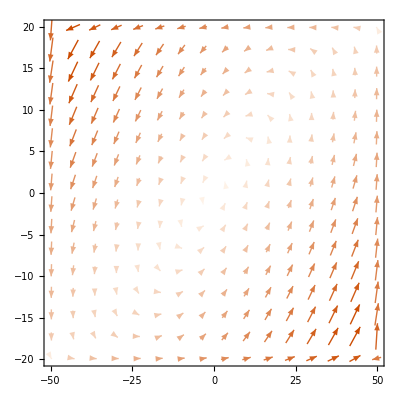

```mathematica
(*Plotting the thermodynamical force field*)
cmapcurrent = (Blend[{RGBColor[{255, 245, 235}/255], RGBColor[{204,76,2}/255]},#]&);
minc= Min[Norm[#]&/@(Transpose[plaquettethermodymaicalforce][[-1]])];
(*maxc =Max[Norm[#]&/@(Transpose[plaquettethermodymaicalforce][[-1]])];*)
maxc=1;

ticklocationsc = N[FindDivisions[{minc, maxc}, 5]];

minc = ticklocationsc[[1]];
maxc = ticklocationsc[[-1]];
stepc = (maxc - minc) /10.;
cmapcurrent2 = cmapcurrent[(#-minc) / (10.*stepc)]&;
ymin=-20;
ymax=20;
xmin=-50;
xmax=50;
xmajor=20;
xminor=0.1;
ymajor=8;
yminor=0.1;
majorlen=0.0;
minorlen=0.0;
ft={Flatten[{Table[{i,MaTeX[i, FontSize->22],{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,MaTeX[j, FontSize->22],{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1],Flatten[{Table[{i,"",{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,"",{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1]};
localforces = Show[
ListVectorPlot[plaquettethermodymaicalforce,
PlotRange-> {{xmin,xmax},{ymin,ymax}},
VectorColorFunction->(cmapcurrent2[#5]&),
VectorColorFunctionScaling->False,
VectorScale->{0.04, Automatic,#5&},
VectorPoints->{16,16},
VectorStyle->{Arrowheads[0.03],Thick}
],
Frame->True,
FrameTicks->ft,
FrameLabel->{
{Framed[MaTeX["x_2",FontSize->28],FrameStyle->None,FrameMargins->{{0,0},{-10,0}},ContentPadding->False],None},
{Framed[MaTeX["x_1",FontSize->28],FrameStyle->None,FrameMargins->{{0,0},{0,-10}},ContentPadding->False],None}
},
ImageSize->400,
AspectRatio->1]
```

```mathematica
(*Plotting the Gillespie simulation trajectory*)
xmax = 50.;
xmin = -50.;
ymax = 20.;
ymin = -20.;
Diffusion = {250.,25.};
h = {100.,40.}/199.;
points = N[Table[{x, y}, {x, xmin, xmax, h[[1]]}, {y, ymin, ymax, h[[2]]}]];
fpoints = Round[Flatten[points, 1],h[[2]]/400000];

Configuration=Import[NotebookDirectory[]<>"../../data/Gillespie.mat"][[1]];
SimulationTime=30000;
pos=Transpose[Configuration];
Simpoints=Table[
fpoints[[pos[[1,i]]]],
{i,1,SimulationTime+1}];
GiespSim=ListPlot[
Simpoints,
Joined->True,
Frame->Transparent,
PlotStyle->{Black,Thickness[0.001]},
PlotRange-> {{-50,50},{-20,20}},
ImageSize->400,
AspectRatio->1];
```

```mathematica
SimExp=Show[
localforces,
GiespSim,
Epilog->{Inset[Text[MaTeX["\\vec{d} = \\vec{F}_{thermo}", FontSize->22]], {32 ,-16}]},
ImagePadding->{{60,10},{50,10}}]
```

-Graphics-

```mathematica
<<MaTeX`
SimExp=Show[
localforces,
GiespSim,
Epilog->{
Inset[
(*Text[MaTeX["\\boldsymbol{j}^\\pi(\\boldsymbol{x})", FontSize->16]*)
Framed[
undistortedGraphicsColumn[
{Graphics[
Text[MaTeX["\\ \\mathbf{d}(\\mathbf{x}) = \\mathbf{F}(\\mathbf{x})", FontSize->20]],
ImageSize->{120, 20}
],
Graphics[{Arrowheads[0.3],Thick,cmapcurrent2[0.7],Arrow[{{0, 0}, {1, 0}}]}, ImageSize->{42, 21}, AspectRatio->18/36]
},
Spacings->-5
],
Background->White,
RoundingRadius->11
],
Scaled[{0.75, 0.12}]
]
},
ImagePadding->{{70,10},{60,10}},
FrameStyle->Thick
]
```

-Graphics-

```mathematica
fest=Interpolation[Chop[plaquettethermodymaicalforce]];
fest[Transpose[Configuration][[2]][[27738]], Transpose[Configuration][[3]][[27738]]];
scalefac = {1.25, 2.5};
f1=scalefac * First[fest[#[[1]]-h[[1]],#[[2]]+h[[2]]]&/@{fpoints[[ Transpose[Configuration][[1]][[27738]]]]}] ;
f2=scalefac *First[fest[#[[1]],#[[2]]+h[[2]]]&/@{fpoints[[ Transpose[Configuration][[1]][[27738]]]]}] ;
f3=scalefac *First[fest[#[[1]]+h[[1]],#[[2]]+h[[2]]]&/@{fpoints[[ Transpose[Configuration][[1]][[27738]]]]}] ;
f4=scalefac *First[fest[#[[1]]-h[[1]],#[[2]]]&/@{fpoints[[ Transpose[Configuration][[1]][[27738]]]]}] ;
f5 =scalefac *First[fest[#[[1]],#[[2]]]&/@{fpoints[[ Transpose[Configuration][[1]][[27738]]]]}] ;
f6=scalefac *First[fest[#[[1]]+h[[1]],#[[2]]]&/@{fpoints[[ Transpose[Configuration][[1]][[27738]]]]}] ;
f7 =scalefac *First[fest[#[[1]]-h[[1]],#[[2]]-h[[2]]]&/@{fpoints[[ Transpose[Configuration][[1]][[27738]]]]}] ;
f8 = scalefac *First[fest[#[[1]],#[[2]]-h[[2]]]&/@{fpoints[[ Transpose[Configuration][[1]][[27738]]]]}] ;
f9 = scalefac *First[fest[#[[1]]+h[[1]],#[[2]]-h[[2]]]&/@{fpoints[[ Transpose[Configuration][[1]][[27738]]]]}] ;

{g1, g2, g3, g4, g5, g6, g7, g8, g9} = Flatten[Table[{yp, xp}, {xp, 2.4, 0.4, -1}, {yp, 0.4, 2.4, 1}], 1];
{j1, j2, j3, j4, j5, j6, j7, j8, j9} = Flatten[Table[{yp, xp}, {xp, 2.5, 0.5, -1}, {yp, 0.5, 2.5, 1}], 1];
```

InterpolatingFunction::dmval: Input value {8.53032,20.4287} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
g3={2.3,2.4};
```

```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts,wasysym, amsbsy}"}];

arrow=Graphics[{FilledCurve[{Line[{{-1.5,0.},{-1.5,0.},{-1.95,1.05},{0.,0.},{0.,-1.05},{0.15,-1.05},{0.15,1.05},{0.,1.05},{0.,0.},{-1.95,-1.05},{-1.5,0.}}]}]}];


(*Zoom in and showing transition between bins. I have trouble giving orange color to a Matx character here.*)
arrowheadsize=0.05;
linethickness = 2;
gridcolor = Gray;
ZoomGispSim=Graphics[
{EdgeForm[{Thick,gridcolor}],FaceForm[],Rectangle[{0, 0}, {1, 1}],
EdgeForm[{Thick,gridcolor}],FaceForm[],Rectangle[{0, 1}, {1, 2}],
EdgeForm[{Thick,gridcolor}],FaceForm[],Rectangle[{0, 2}, {1, 3}],
EdgeForm[{Thick,gridcolor}],FaceForm[],Rectangle[{1, 0}, {2, 1}],
EdgeForm[{Thick,gridcolor}],FaceForm[],Rectangle[{2, 0}, {3, 1}],
EdgeForm[{Thick,gridcolor}],FaceForm[],Rectangle[{1, 1}, {2, 2}],
EdgeForm[{Thick,gridcolor}],FaceForm[],Rectangle[{1, 2}, {2, 3}],
EdgeForm[{Thick,gridcolor}],FaceForm[],Rectangle[{2, 1}, {3, 2}],
EdgeForm[{Thick,gridcolor}],FaceForm[],Rectangle[{2, 2}, {3, 3}],

Arrowheads[arrowheadsize],AbsoluteThickness[linethickness],Arrow[{{1.5,3},{1.5,2.6}}],
Arrowheads[arrowheadsize],AbsoluteThickness[linethickness],Arrow[{{1.5,2.4},{1.5,1.6}}],
Arrowheads[arrowheadsize],AbsoluteThickness[linethickness],Arrow[{{1.4,1.5},{0.6,1.5}}],
Arrowheads[arrowheadsize],AbsoluteThickness[linethickness],Arrow[{{0.5,1.4},{0.5,0.6}}],
Arrowheads[arrowheadsize],AbsoluteThickness[linethickness],Arrow[{{0.6,0.5},{1.4,0.5}}],
Arrowheads[arrowheadsize],AbsoluteThickness[linethickness],Arrow[{{1.6,0.5},{2.4,0.5}}],
Arrowheads[0],AbsoluteThickness[linethickness],Arrow[{{2.6,0.5},{3,0.5}}],

cmapcurrent2[0.6],Arrowheads[0.06],AbsoluteThickness[4],Dashing[None],Arrow[{g3,g3+f3}],
cmapcurrent2[0.6],Arrowheads[0.06],AbsoluteThickness[4],Dashed,Arrow[{g3,g3+f3*{1,0}}],
cmapcurrent2[0.6],Arrowheads[0.06],AbsoluteThickness[4],Dashed,Arrow[{g3,g3+f3*{0,1}}],

cmapcurrent2[0.6],Arrowheads[0.06],AbsoluteThickness[4],Dashed,Arrow[{{1.4, 3},j2+f2*{0,1}+{-0.1,- 0.15}+{0,1}}],
cmapcurrent2[0.6],Arrowheads[0.06],AbsoluteThickness[4],Dashed,Arrow[{j2 +{-0.1, -0.15},j2+f2*{0,1}+{-0.1,- 0.15}}],
cmapcurrent2[0.6],Arrowheads[0.06],AbsoluteThickness[4],Dashed,Arrow[{j4 +{-0.1, -0.15},j4+f4*{0,1}+{-0.1,- 0.15}}],
cmapcurrent2[0.6],Arrowheads[0.06],AbsoluteThickness[4],Dashed,Arrow[{j5 +{-0.25, 0.1},j5+f5*{1,0}+{-0.25, 0.1}}],
cmapcurrent2[0.6],Arrowheads[0.06],AbsoluteThickness[4],Dashed,Arrow[{j7 + {0.75, 0.1},j7+f7*{1,0}+{0.75, 0.1}}],
cmapcurrent2[0.6],Arrowheads[0.06],AbsoluteThickness[4],Dashed,Arrow[{j8 + {0.75, 0.1},j8+f8*{1,0}+{0.75, 0.1}}],

cmapcurrent2[0.6],Arrowheads[0.06],AbsoluteThickness[4],Dashed,Arrow[{{3, 0.6},j9+f9*{1,0}+{0.75, 0.1}}],

Opacity[1, Black],Arrowheads[{{0.015,1,arrow},{-0.015,0,arrow}}], AbsoluteThickness[2], Dashing[None], Arrow[{{3.25, 2.5}, {3.25, 1.5}}],
Opacity[1, Black],Arrowheads[{{0.015,1,arrow},{-0.015,0,arrow}}], AbsoluteThickness[2], Dashing[None], Arrow[{{1.5, -0.25}, {2.5, -0.25}}]
},
ImageSize->400,
ImagePadding->{{10,50},{50,10}},
Epilog->{
Inset[Text[MaTeX["\\mathbf{d}(\\blacktriangle)", FontSize->22], Background->White], {2.05, 1.65}],
Inset[Text[MaTeX["h_2 d_{\\circ,\\blacktriangle}", FontSize->22]], {2.65, 2.15}],
Inset[Text[MaTeX["h_1 d_{\\lozenge,\\blacktriangle}", FontSize->22],Background->White], {2.1, 2.6}],
Inset[Text[MaTeX["\\CIRCLE", FontSize->22]], {0.5, 2.5}],
Inset[Text[MaTeX["\\lozenge", FontSize->22]], {1.5, 2.5}],
Inset[Text[MaTeX["\\blacktriangle", FontSize->22]], {2.5, 2.5}],
Inset[Text[MaTeX["\\square", FontSize->22]], {0.5, 1.5}],
Inset[Text[MaTeX["\\bigstar", FontSize->22]], {1.5, 1.5}],
Inset[Text[MaTeX["\\Circle", FontSize->22]], {2.5,1.5}],
Inset[Text[MaTeX["\\blacklozenge", FontSize->22]], {0.5, 0.5}],
Inset[Text[MaTeX["\\vartriangle", FontSize->22]], {1.5, 0.5}],
Inset[Text[MaTeX["\\blacksquare", FontSize->22]], {2.5, 0.5}],
Inset[Text[MaTeX["h_2", FontSize->24]], {3.4, 2}],
Inset[Text[MaTeX["h_1", FontSize->24]], {2, -0.4}]
(*the color setting do not have orange, I can't put d_{y,z} in orange*)
(*,Inset[Text[MaTeX["{\\rm}\\color{orange}d_{y,z} {\\rm}", FontSize->18]], {1.65, 2.15}]*)
}
]
```

-Graphics-

```mathematica
(*Zoom in the scalar current*)
(*We might need to decide the notation for time*)
xposition1 = Transpose[Configuration][[2]][[27737]];
xposition2 = Transpose[Configuration][[2]][[27738]];
xposition3 = Transpose[Configuration][[2]][[27739]];
xposition4 = Transpose[Configuration][[2]][[27740]];
xposition5 = Transpose[Configuration][[2]][[27741]];
xposition6 = Transpose[Configuration][[2]][[27742]];
yposition1 = Transpose[Configuration][[3]][[27737]];
yposition2 = Transpose[Configuration][[3]][[27738]];
yposition3 = Transpose[Configuration][[3]][[27739]];
yposition4 = Transpose[Configuration][[3]][[27740]];
yposition5 = Transpose[Configuration][[3]][[27741]];
yposition6 = Transpose[Configuration][[3]][[27742]];
label1=MaTeX["t_i", FontSize->14];
label2=MaTeX["t_{i+1}", FontSize->14];
label3=MaTeX["t_{i+2}", FontSize->14];
label4=MaTeX["t_{i+3}", FontSize->14];
label5=MaTeX["t_{i+4}", FontSize->14];
label6=MaTeX["t_{i+5}", FontSize->14];
longticksize = 0.01;
shortticksize = 0.0025;
bottomticks = {{xposition1, label1, {longticksize, 0}}, {xposition2, label2, {longticksize, 0}},{xposition3, label3, {longticksize, 0}},{xposition4, label4, {longticksize, 0}},{xposition5, label5, {longticksize, 0}},{xposition6, label6, {longticksize, 0}}};
ft = {bottomticks, Automatic, None, None};
```

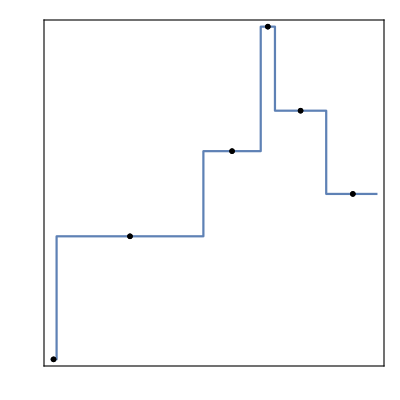

```mathematica
leftpts = Transpose[Transpose[{Transpose[Configuration][[2]],Transpose[Configuration][[3]]}][[27737;;27743]]][[1]][[1;;-2]];
rightpts = Transpose[Transpose[{Transpose[Configuration][[2]],Transpose[Configuration][[3]]}][[27737;;27743]]][[1]][[2;;-1]];
rightpts = Min[#, 8.5324]&/@rightpts;
midpts = (leftpts + rightpts)/2;
pts2plot = Transpose[{midpts, Transpose[Transpose[{Transpose[Configuration][[2]],Transpose[Configuration][[3]]}][[27737;;27743]]][[2]][[1;;-2]]}];
pms = MaTeX[#, FontSize->18]&/@{"\\lozenge", "\\bigstar", "\\square", "\\blacklozenge", "\\vartriangle", "\\blacksquare"};
ZoomJdSim=Show[
ListStepPlot[
Transpose[{Transpose[Configuration][[2]],Transpose[Configuration][[3]]}][[27737;;27742]],
PlotStyle->{Thickness[0.004]},
PlotMarkers->None
],
ListPlot[{#}&/@pts2plot,
PlotStyle->Black,
PlotMarkers->pms
],
Frame->True,
ImageSize-> 400,
ImagePadding->{{10,50},{50,10}},
FrameTicks->(*ft*)None,
AspectRatio->1(*,
FrameLabel->{MaTeX["\\text{Time} \\quad T(or)\\tau",FontSize->16],MaTeX["\\text{Scalar Current} \\quad J_d",FontSize->16]}*)
]
```

```mathematica
ZoomJdSim=Show[ZoomJdSim,
ImagePadding->{{10,70},{60,10}},
Epilog-> {
(*Inset[Text[MaTeX["i\\rightarrow{j}", FontSize->16]],{8.5315,20.33}],
Inset[Text[MaTeX["J_d=J_d+d_{i,j}", FontSize->16]], {8.532,20.33}],*)
cmapcurrent2[0.6],Arrowheads[0.06],AbsoluteThickness[4],Dashed,Arrow[{{xposition2,yposition1},{xposition2,yposition2}}],
cmapcurrent2[0.6],Arrowheads[0.06],AbsoluteThickness[4],Arrow[{{xposition3,yposition2},{xposition3,yposition3}}],
cmapcurrent2[0.6],Arrowheads[0.06],AbsoluteThickness[4],Arrow[{{xposition4,yposition3},{xposition4,yposition4}}],
cmapcurrent2[0.6],Arrowheads[0.06],AbsoluteThickness[4],Arrow[{{xposition5,yposition4},{xposition5,yposition5}}],
cmapcurrent2[0.6],Arrowheads[0.06],AbsoluteThickness[4],Arrow[{{xposition6,yposition5},{xposition6,yposition6}}],

Inset[Text[MaTeX["d_{\\bigstar, \\lozenge}", FontSize->22]], Scaled[{0.12, 0.2}]],
Inset[Text[MaTeX["d_{\\square, \\bigstar}", FontSize->22]], Scaled[{0.39, 0.5}]],
Inset[Text[MaTeX["d_{\\blacklozenge, \\square}", FontSize->22]], Scaled[{0.56, 0.8}]],
Inset[Text[MaTeX["d_{\\vartriangle, \\blacklozenge}", FontSize->22]], Scaled[{0.76, 0.86}]],
Inset[Text[MaTeX["d_{\\blacksquare, \\vartriangle}", FontSize->22]], Scaled[{0.91, 0.63}]]
},
FrameStyle->Thick
]
```

-Graphics-

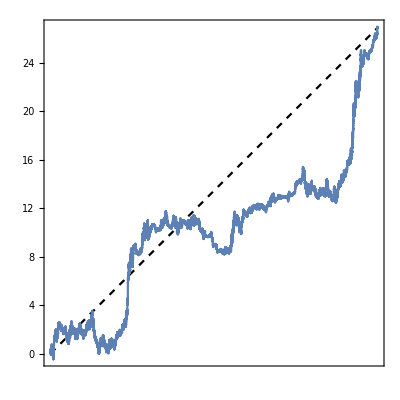

```mathematica
(*The scalar current for the simulation trajectory. The defination of j_d (little j) seems incorrect here, should we just take it out with the dashed line?*)
<<MaTeX`
JdSim=Show[
ListPlot[
{{0,0},Transpose[{Transpose[Configuration][[2]],Transpose[Configuration][[3]]}][[-1]]},
PlotStyle->{Dashed,Black},
Joined->True
],
ListPlot[
Transpose[{Transpose[Configuration][[2]],Transpose[Configuration][[3]]}],
Joined->True
],
PlotRange->All,
Epilog->{Inset[Rotate[Text[MaTeX["\\text{Slope } j_{\\mathbf d}", FontSize->26]], 45 Degree], {7.45, 23.25}]},
Frame->True,
ImageSize->  400,
ImagePadding->{{70,10},{60,10}},
AspectRatio->1,
FrameLabel->{
{Framed[MaTeX["\\text{Accumulated Current}",FontSize->28],FrameStyle->None,FrameMargins->{{0,0},{-10,0}},ContentPadding->False],None},
{Framed[MaTeX["",FontSize->20],FrameStyle->None,FrameMargins->{{0,0},{0,-8}},ContentPadding->False],None}
},
FrameTicks->{{{0, MaTeX["0", FontSize->30]}, {Transpose[Configuration][[2]][[-1]]-0.12, MaTeX["\\tau_{\\rm obs}", FontSize->30]}}, {}, {}, {}},
Prolog->{
Inset[
Show[
Plot[
Exp[-x^2], {x, -5, 5},
Frame->True,
ImageSize->175,
PlotStyle->Thick,
FrameLabel->{MaTeX["j_{\\mathbf d}",FontSize->22],MaTeX["P(j_{\\mathbf d})",FontSize->22]},
PlotRange->{{-6, 6}, {0, 1.25}},
Axes->False,
FrameStyle->Thick
],
Graphics[
{
Opacity[1, Black],Arrowheads[0.1], AbsoluteThickness[2], Dashing[None], Arrow[{{-3, 0.5}, {-1,0.5}}],
Opacity[1, Black],Arrowheads[0.1], AbsoluteThickness[2], Dashing[None], Arrow[{{3, 0.5}, {1,0.5}}],
Inset[Text[MaTeX["\\text{Var}(j_{\\mathbf d})", FontSize->20]], {3.3, 0.7}]
}
],
FrameTicks->{{}, {},{{0, MaTeX["\\langle j_{\\mathbf d} \\rangle", FontSize->22], 0.08}}, {}}
],
Scaled[{0.275, 0.75}]
]
},
FrameStyle->Thick
]
```

```mathematica
patch1=undistortedGraphicsRow[{SimExp,ZoomGispSim},Spacings->100]
```

-Graphics-

```mathematica
patch2=undistortedGraphicsRow[{JdSim,ZoomJdSim},Spacings->100]
```

-Graphics-

```mathematica
Zoompatch1=Show[patch1,
Epilog-> {
EdgeForm[{Thickness[0.001],Black}],FaceForm[],Rectangle[{199, 333}, {206, 340}],
Thick, Gray,Line[{{206,340},{515,383.5}}],
FaceForm[],Line[{{206,333},{515,82}}]
}
]
```

-Graphics-

```mathematica
Zoompatch2=Show[patch2,
Epilog-> {
EdgeForm[{Thickness[0.001],Black}],FaceForm[],Rectangle[{358, 302}, {368, 312}],
Thick, Gray,Line[{{368,312},{508,380}}],
Thick, Gray,Line[{{368,302},{508,61}}]
}
]
```

-Graphics-

```mathematica
fig3=Show[
undistortedGraphicsColumn[{Zoompatch1,Zoompatch2}],
Epilog->{
Inset[Text[MaTeX["\\text{(a)}", FontSize->30]], Scaled[{0.02, 0.975}]],
Inset[Text[MaTeX["\\text{(b)}", FontSize->30], Background->White], Scaled[{0.52, 0.975}]],
Inset[Text[MaTeX["\\text{(c)}", FontSize->30]], Scaled[{0.02, 0.475}]],
Inset[Text[MaTeX["\\text{(d)}", FontSize->30], Background->White], Scaled[{0.52, 0.475}]]
}
]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"Fig3.pdf", fig3];
Export[NotebookDirectory[]<>"../Fig3.pdf", fig3];
```